## EdgesOnTop-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51i (18 June 2017)) loaded Sun 18 Jun 2017 18:12:19
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

There are 8 cells in the tissue.

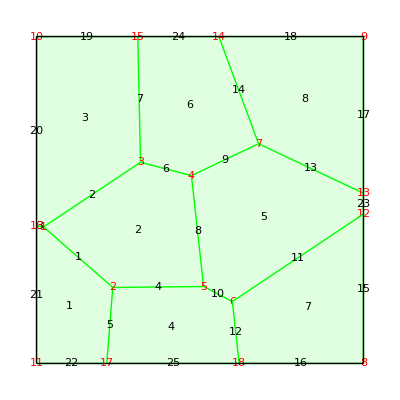

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Green,Thick], "EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

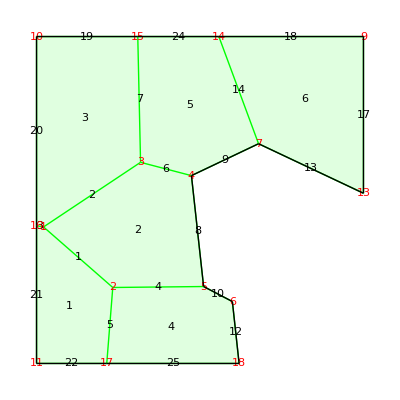

```mathematica
R=DeleteCell[Q, 5];
R=DeleteCell[R, 7];
S=DTissue2Tissue[R];
ShowTissue[S, "CellNumbers"-> True, "EdgeStyles"-> Directive[Green,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

```mathematica
VerticesOnTop[S]
```

{6,10,15,14,9}

```mathematica
CellsOnLeft[S]
```

{1,3}

```mathematica
CellsOnBottom[S]
```

{1,4,6}

```mathematica
EdgesOnTop[S]
```

{18,19,24}

```mathematica
EdgesOnLeft[S]
```

{20,21}

```mathematica
VerticesOnLeft[S]
```

{11,16,10}

```mathematica
CellsOnBottom[S]
```

{1,4,6}